```mathematica
foo=Table[Probability[Z≥3,Z\[Distributed]BinomialDistribution[δ,(M-1)/M]],{δ,6,15}]
```

{((-1+M)^3 (10+6 M+3 M^2+M^3))/M^6,((-1+M)^3 (15+10 M+6 M^2+3 M^3+M^4))/M^7,((-1+M)^3 (21+15 M+10 M^2+6 M^3+3 M^4+M^5))/M^8,((-1+M)^3 (28+21 M+15 M^2+10 M^3+6 M^4+3 M^5+M^6))/M^9,((-1+M)^3 (36+28 M+21 M^2+15 M^3+10 M^4+6 M^5+3 M^6+M^7))/M^10,((-1+M)^3 (45+36 M+28 M^2+21 M^3+15 M^4+10 M^5+6 M^6+3 M^7+M^8))/M^11,BetaRegularized[(-1+M)/M,3,10],BetaRegularized[(-1+M)/M,3,11],BetaRegularized[(-1+M)/M,3,12],BetaRegularized[(-1+M)/M,3,13]}

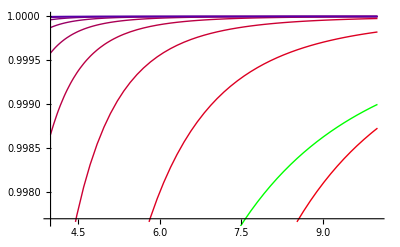

```mathematica
Show[
Plot[foo,{M,4,10},PlotStyle->Table[Blend[{Red,Blue},δ/15],{δ,1,15}]],
Plot[1-1/M^3,{M,4,10},PlotStyle->{Thick,Green}]
]
```